## Skybox

```mathematica
img=Import[NotebookDirectory[]<>"TropicalSunnyDay.png"]
```

-Graphics-

```mathematica
(* +X,-X,+Y,-Y,+Z,-Z *)
```

```mathematica
(sun=ImageTake[img,All,{2048*5+1,-1}])//ImageDimensions
```

{2048,2048}

```mathematica
ImageTake[sun,{600,710},{1340,1450}]
```

-Graphics-

## Sun Direction

```mathematica
(* Default: +Z *)
```

```mathematica
elev=1024-1/2(600+710);orient=1/2(1340+1450)-1024;
```

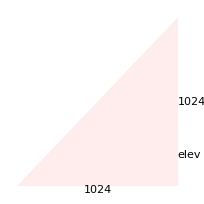

```mathematica
Graphics[{LightPink,EdgeForm[Thin],
Triangle[{{0,0},{1024,0},{1024,1024}}],
Triangle[{{0,0},{1024,0},{1024,elev}}],
Black,
Text[1024,{512,0},{0,1.5}],
Text[1024,{1024,512},{-1.5,0}],
Text["elev",{1024,elev/2},{-1.5,0}]
}]
```

```mathematica
N[ArcTan[elev/1024]/°]
```

19.8167

```mathematica
N[ArcTan[orient/1024]/°]
```

19.9157

## Waveform

```mathematica
Clear[f];x=.;y=.;
f=0;

For[i=1,i<100,i++,
φ=RandomReal[2π];
ϕ=RandomReal[2π];
k=0.5i;
f+=Sqrt[Exp[-1/(k)^2]/k^3 Abs[Cos[φ]]^2]Sin[k Cos[φ]x+k Sin[φ]y+ϕ];
];
```

```mathematica
Plot3D[f,{x,-10,10}, {y,-10,10},PlotPoints->50,BoxRatios->Automatic,Mesh->None]
```

-Graphics3D-

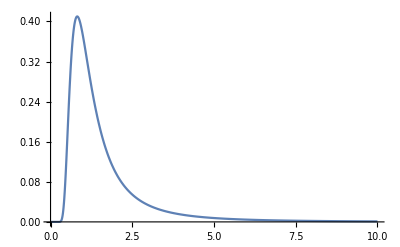

```mathematica
Plot[Exp[-1/(k )^2]/k^3,{k,0,10},PlotRange->All]
```

```mathematica
NN=64;g=9.8;V=5;
(*dmax*)(π NN V^2/g)/4
```

128.228

```mathematica
N[20/512]
```

0.0390625

```mathematica
N[10/128]
```

0.078125

## Water Color

```mathematica
λ={470,530,700}
```

{470,530,700}

```mathematica
loss2alpha[loss_]:=-Log[1-loss]
```

```mathematica
loss2alpha[.02]
```

0.0202027

```mathematica
N[(λ/λ⟦1⟧)^-1 256]
```

{256.,227.019,171.886}

```mathematica
Log[1-0.55]/Log[1-0.11]
```

6.85215

```mathematica
Log[1-0.11]
```

-0.116534

```mathematica
Integrate[Exp[-α(h+l(1-Sin[ϕ]))],{l,0,L}]
```

(ⅇ^(-α (h-L sin(ϕ)+L))-ⅇ^(α (-h)))/(α (sin(ϕ)-1))

## Terrain

```mathematica
Clear[ω,ϕ,g,n];
```

```mathematica
ω[t_]:=-6 Abs[t]^5+15 Abs[t]^4-10 Abs[t]^3+1/;t≥-1&&t≤1
ω[t_]:=0/;t>1||t<-1
```

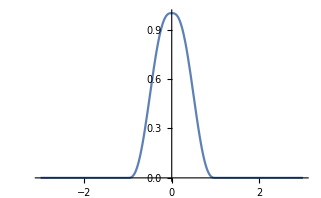

```mathematica
Plot[ω[t],{t,-3,3}]
```

```mathematica
P=Permutations[Range[8]]⟦RandomInteger[8!]⟧
ϕ[i_]:=P⟦Mod[i,8,1]⟧;
G=({{1, 0}, {1/√2, 1/√2}, {0, 1}, {-1/√2, 1/√2}, {-1, 0}, {-1/√2, -1/√2}, {0, -1}, {1/√2, -1/√2}});
```

{7,4,6,1,2,3,5,8}

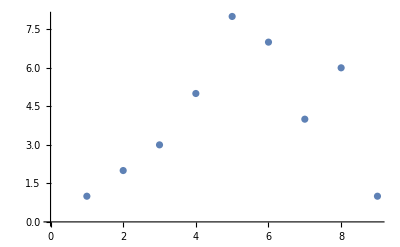

```mathematica
ListPlot@Table[ϕ[i],{i,-4,4}]
```

```mathematica
g[i_,j_]:=G⟦ϕ[i+ϕ[j]]⟧;
```

```mathematica
n[x_,y_]:=∑_(i=Floor[x])^(Floor[x]+1) ∑_(j=Floor[y])^(Floor[y]+1) ω[x-i]ω[y-j]g[i,j].{x-i,y-j}
```

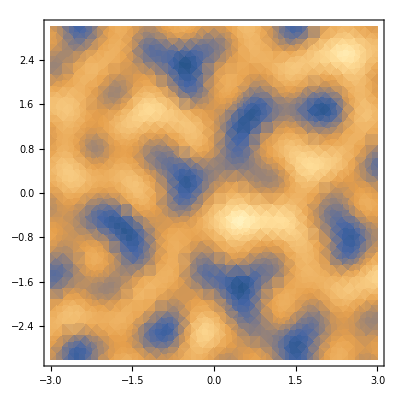

```mathematica
DensityPlot[n[x,y],{x,-3,3},{y,-3,3}]
```

```mathematica
Clear[nt];
nt=Compile[{{x,_Real},{y,_Real}},∑_(i=0)^10 n[2^i x,2^i y]/2^i]
```

CompiledFunction[…]

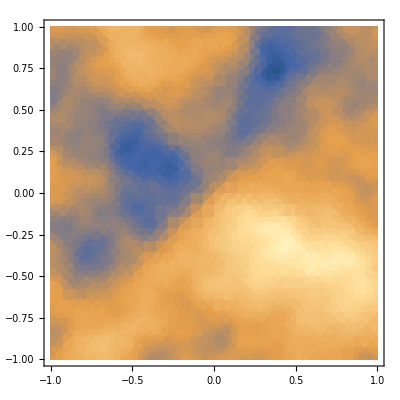

```mathematica
DensityPlot[nt[x,y],{x,-1,1},{y,-1,1}]
```

```mathematica
ListPlot3D[
Table[nt[x,y],{x,-3,3,0.1},{y,-3,3,0.1}],
InterpolationOrder->2,
BoxRatios->{1,1,0.05},
Boxed->False,
Lighting->{{"Directional", LightBlue, {0, 3, 3}}},
PlotRange->{-0.7,0.7},
Axes->False,
Mesh->None
]
```

-Graphics3D-